## Initialization Section

```mathematica
SetDirectory[NotebookDirectory[]]
<<MaTeX`
ConfigureMaTeX["Ghostscript" -> FileNameJoin[{"C:","Program Files","gs","gs9.19","bin","gswin64c.exe"}]]
```

C:\Users\Matthew\Documents\RbPapers\MBL_Critical_Behavior\figures\cartoons

{pdfLaTeX→C:\Program Files (x86)\MiKTeX 2.9\miktex\bin\pdflatex.exe,CacheSize→100,Ghostscript→C:\Program Files\gs\gs9.19\bin\gswin64c.exe}

```mathematica
SFColor={92,129,182}/256;
MIColor={235,98,48}/256;
QColor={225,156,38}/256;
LColor={146,149,151}/256;
green=CMYKColor[0.2883,0.055,0.4036,0];
pink=CMYKColor[0.0435,0.2683,0.2949,0];
blue=CMYKColor[0.355,0.1076,0.0982,0];
atomgreen= RGBColor[0.8, 1,0.2];
ColorData[97,"ColorList"];
QPLC=ColorData[94,"ColorList"]⟦1⟧;
AtomColor=ColorData[97,"ColorList"]⟦3⟧;
markerMI=Graphics[{RGBColor[MIColor],Disk[]}];
SetDirectory[NotebookDirectory[]];
```

```mathematica
Gauss[x_,m_,s_]:=1/(√(2 π s^2))Exp[(-(x-m)^2)/(2 s^2)]
```

```mathematica
ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Directive[GrayLevel[.3],Arrowheads[{{-0.05,0},{0.05,1}}]]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]
```

```mathematica
GenerateSpikeBall[loc_,radius_,disorderFrac_]:=Module[{Nspikes,ii,rvals,θvals,spikes,ctrlPtLists,allPts,peakOrValley,NctrlPts},
Nspikes=25;

NctrlPts=2Nspikes-1;
θvals=Subdivide[0,2π,NctrlPts-1];
For[ii=1,ii≤Length[θvals],ii++,
θvals⟦ii⟧=θvals⟦ii⟧+RandomReal[{-1,1}(2π)/NctrlPts disorderFrac/2];];
θvals=Sort[θvals];

rvals=ConstantArray[radius,{Length[θvals]}];
peakOrValley=1;
For[ii=1,ii≤Length[rvals],ii++,
randScalar=If[peakOrValley==1,
RandomReal[{Min[{1.2rvals⟦Mod[ii-1,NctrlPts,1]⟧,0.9radius}],radius(1+disorderFrac)}],
RandomReal[{radius(1-disorderFrac),Max[{0.8rvals⟦Mod[ii-1,NctrlPts,1]⟧,1.1radius}]}]];
rvals⟦ii⟧=rvals⟦ii⟧randScalar;
peakOrValley=Mod[peakOrValley+1,2];
];
θvals⟦-1⟧=θvals⟦1⟧;
rvals⟦-1⟧=rvals⟦1⟧;

allPts=Table[rvals⟦ii⟧{Cos[θvals⟦ii⟧],Sin[θvals⟦ii⟧]}+loc,{ii,1,Length[θvals]}];
ctrlPtLists=Table[allPts⟦Mod[ii+{0,1,2},NctrlPts,1]⟧,{ii,1,Length[θvals]-2,2}];
spikes=Table[BSplineCurve[ctrlPtLists⟦ii⟧],{ii,1,Length[ctrlPtLists]}];
Return[spikes];
];
```

## Localization Length Growth: Cartoon Fig. 2

```mathematica
diskgreen= RGBColor[0.7, 0.85,0.2];
SpikeBallRed=ColorData[93,"ColorList"]⟦1⟧;
QPLC=ColorData[94,"ColorList"]⟦1⟧;

GR=(1+√5)/2;
Phi=0.16;
WD=0.8;
SmoothBox[x_,w_,dw_]:=1/π(ArcTan[(x+w)/dw]-ArcTan[(x-w)/dw])
DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 
DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)

Graphics[{GenerateSpikeBall[{0,0},0.55,0.85],GenerateSpikeBall[{2,0},0.75,0.25],GenerateSpikeBall[{4,0},0.75,0.1]}]

LW=0.13;
LW2=0.17;
LW3=0.18;
WlenR=4.15;
atomR=0.10;
atomShdwR=0.13;
Uo=0.15*0.8/0.5;
Ur=0.065;
FntSz=18;
ExpPlotOff=0.85;
ExpPlotFillOp=0.4;
```

-Graphics-

0.6

{1,1}

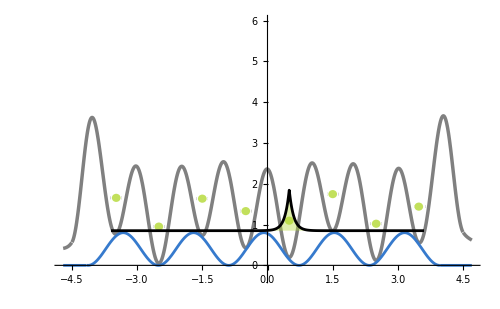

Fig2cT0_v2.pdf

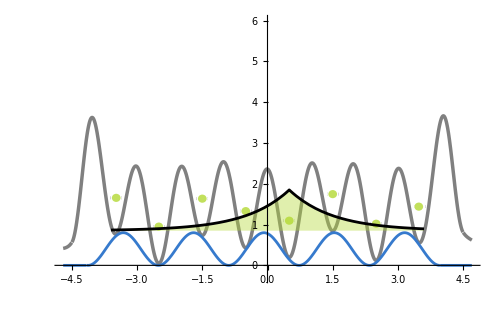

Fig2cT1_v2.pdf

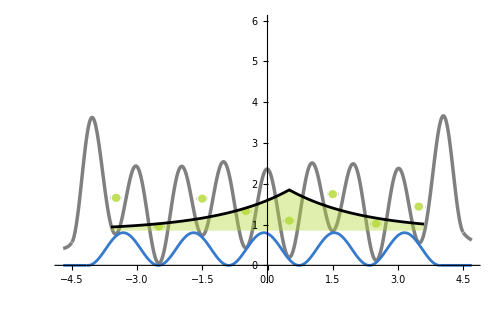

Fig2cT10_v2.pdf

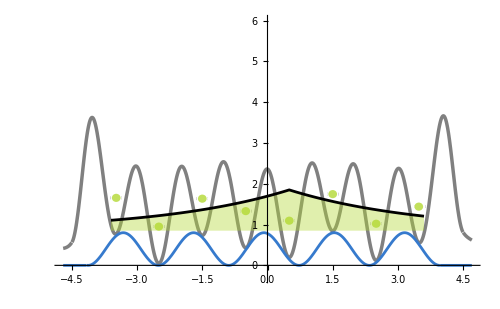

Fig2cT100_v2.pdf

```mathematica
EXPPlotT100=Plot[
Exp[-Abs[x-0.5]/3]+ExpPlotOff,
{x,-3.6,3.6},
PlotRange-> {{-3.6,3.6},{-0.3,6}},
PlotStyle-> {RGBColor[{0,0,0}],Thickness[0.004]},
AxesStyle-> Opacity[0],
Filling-> ExpPlotOff,
FillingStyle-> {Directive[Opacity[ExpPlotFillOp],diskgreen]}
];
EXPPlotT10=Plot[
Exp[-Abs[x-0.5]/1.7]+ExpPlotOff,
{x,-3.6,3.6},
PlotRange-> {{-3.6,3.6},{-0.3,6}},
PlotStyle-> {RGBColor[{0,0,0}],Thickness[0.004]},
AxesStyle-> Opacity[0],
Filling-> ExpPlotOff,
FillingStyle-> {Directive[Opacity[ExpPlotFillOp],diskgreen]}
];
EXPPlotT1=Plot[
Exp[-Abs[x-0.5]/1]+ExpPlotOff,
{x,-3.6,3.6},
PlotRange-> {{-3.6,3.6},{-0.3,6}},
PlotStyle-> {RGBColor[{0,0,0}],Thickness[0.004]},
AxesStyle-> Opacity[0],
Filling-> ExpPlotOff,
FillingStyle-> {Directive[Opacity[ExpPlotFillOp],diskgreen]}
];
EXPPlotT0=Plot[
Exp[-Abs[x-0.5]/0.1]+ExpPlotOff,
{x,-3.6,3.6},
PlotRange-> {{-3.6,3.6},{-0.3,6}},
PlotStyle-> {RGBColor[{0,0,0}],Thickness[0.004]},
AxesStyle-> Opacity[0],
Filling-> ExpPlotOff,
FillingStyle-> {Directive[Opacity[ExpPlotFillOp],diskgreen]}
];
(*
AtomListALT0=Graphics[{ 
diskgreen,
{Opacity[0.01],Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]},
{Opacity[0.05],Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}]},
{Opacity[0.1],Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}]},
{Opacity[0.2],Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}]},
{Opacity[0.9],Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}]},
{Opacity[0.2],Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}]},
{Opacity[0.1],Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}]},
{Opacity[0.05],Disk[{3.48,0.95+DisordF[3.5]},{atomR,atomR}]}
}];
AtomListALT1=Graphics[{ 
diskgreen,
{Opacity[0.05],Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]},
{Opacity[0.1],Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}]},
{Opacity[0.4],Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}]},
{Opacity[0.6],Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}]},
{Opacity[0.6],Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}]},
{Opacity[0.4],Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}]},
{Opacity[0.1],Disk[{3.48,0.95+DisordF[3.5]},{atomR,atomR}]}
}];
AtomListALT10=Graphics[{ 
diskgreen,
{Opacity[0.1],Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]},
{Opacity[0.4],Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}]},
{Opacity[0.6],Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}]},
{Opacity[0.7],Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}]},
{Opacity[0.7],Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}]},
{Opacity[0.6],Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}]},
{Opacity[0.3],Disk[{3.48,0.95+DisordF[3.5]},{atomR,atomR}]}
}];
AtomListALT100=Graphics[{ 
diskgreen,
{Opacity[0.3],Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]},
{Opacity[0.5],Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}]},
{Opacity[0.6],Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}]},
{Opacity[0.7],Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}]},
{Opacity[0.7],Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}]},
{Opacity[0.7],Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}]},
{Opacity[0.6],Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}]},
{Opacity[0.5],Disk[{3.48,0.95+DisordF[3.5]},{atomR,atomR}]}
}];

AtomListShadowAL=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{-3.48,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}
}];
*)
AtomListALT0=Graphics[{ 
diskgreen,
{Opacity[0.8],Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{3.48,0.95+DisordF[3.5]},{atomR,atomR}]}
}];
AtomListALT1=Graphics[{ 
diskgreen,
{Opacity[0.8],Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{3.48,0.95+DisordF[3.5]},{atomR,atomR}]}
}];
AtomListALT10=Graphics[{ 
diskgreen,
{Opacity[0.8],Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{3.48,0.95+DisordF[3.5]},{atomR,atomR}]}
}];
AtomListALT100=Graphics[{ 
diskgreen,
{Opacity[0.8],Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{3.48,0.95+DisordF[3.5]},{atomR,atomR}]}
}];

AtomListShadowAL=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{-3.48,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}
}];
GM=0.6
barelattV2=Plot[{GM Gauss[x,-4.1,0.2]+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+GM Gauss[x,4.1,0.2]+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];

QP=Plot[{(DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {Directive[Thickness[0.004],QPLC]
}];

WLevels = Graphics[{Thickness[0.004],
QPLC,
Opacity[0.8],
Dashing[0.008],
Line[{{(2 π-Phi)/(π (GR-1)),WD},{WlenR,WD}}]
}];


DLevels= Graphics[{Thickness[0.004],
RGBColor["Black"],
Opacity[0.4],
Dashing[0.008],
Line[{{-0.5- LW3,0.95+DisordF[-1.5]},{-0.5+ LW3,0.95+DisordF[-1.5]}}],
Line[{{-2.5 - LW3,0.95+DisordF[-1.5]},{-2.5+ LW3,0.95+DisordF[-1.5]}}]
}];

arcsSS=Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-2,DisordF[1.5]+1.2}],
Inset[arcsWArrows[rdsAndAngls],{-1,DisordF[1.5]+1.2}]
}];
WArrows=Graphics[{Thickness[0.003],
QPLC,
{Arrowheads[0.022],Arrow[{{WlenR,0},{WlenR,WD}}]},
{Arrowheads[0.022],Arrow[{{WlenR,WD},{WlenR,0}}]}
}];


PillTxy={1,1}
PillLabels2=Graphics[{
Inset[MaTeX["\\mathbf |\\mathrm{N_A=4} \\mathbf \\rangle",Magnification->1.8],{-1,PillTxy⟦2⟧+0.5+0.15}]
}];

labelsa={Graphics[{
{QPLC,Text[Style[ToExpression["W",TeXForm,HoldForm],FntSz],{4.075,0.8},{0,-1}]}
}]};


CartoonTimeT0=Show[barelattV2,
LevelList,
QP,
AtomListShadowAL,AtomListALT0,
EXPPlotT0]
Export["Fig2cT0_v2.pdf",%,Rasterize-> False,ImageSize-> 30mm]

CartoonTimeT1=Show[barelattV2,
LevelList,
QP,
AtomListShadowAL,AtomListALT1,
EXPPlotT1]
Export["Fig2cT1_v2.pdf",%,Rasterize-> False,ImageSize-> 30mm]

CartoonTimeT10=Show[barelattV2,
LevelList,
QP,
AtomListShadowAL,AtomListALT10,
EXPPlotT10]
Export["Fig2cT10_v2.pdf",%,Rasterize-> False,ImageSize-> 30 mm]

CartoonTimeT100=Show[barelattV2,
LevelList,
QP,
AtomListShadowAL,AtomListALT100,
EXPPlotT100]
Export["Fig2cT100_v2.pdf",%,Rasterize-> False,ImageSize->30mm]
```

```mathematica
2 N[1/Exp[1]]
```

0.735759

```mathematica
N[30/9]/2
N[30/9]/2+N[30/9]
N[30/9]/2+2 N[30/9]
N[30/9]/2+3 N[30/9]
N[30/9]/2+4 N[30/9]
N[30/9]/2+5 N[30/9]
N[30/9]/2+6 N[30/9]
N[30/9]/2+7 N[30/9]
N[30/9]/2+8 N[30/9]
```

1.66667

5.

8.33333

11.6667

15.

18.3333

21.6667

25.

28.3333